```mathematica
ClearAll["Global`*"]
```

```mathematica
nc = 3;
nf = 3;
cf = (nc^2-1)/2/nc;
orderbeta = 3;
numPrec = 20;
```

## Beta

```mathematica
betarule:=Module[{beta={11/2-nf/3,51/4-19/12*nf,2857/64-5033/576*nf+325/1728*nf^2,149753/768+891/32*Zeta[3]-(1078361/20736+1627/864*Zeta[3])*nf+(50065/20736+809/1296*Zeta[3])*nf^2+1093/93312*nf^3,2/4^5*(8157455/16+621885/2*Zeta[3]-88209/2*Zeta[4]-288090*Zeta[5]+nf*(-336460813/1944-4811164/81*Zeta[3]+33935/6*Zeta[4]+1358995/27*Zeta[5])+nf^2*(25960913/1944+698531/81*Zeta[3]-10526/9*Zeta[4]-381760/81*Zeta[5])+nf^3*(-630559/5832-48722/243*Zeta[3]+1618/27*Zeta[4]+460/9*Zeta[5])+nf^4*(1205/2916-152/81*Zeta[3]))}},Join[Table[b[n]->beta[[n]],{n,1,Length[beta]}],Table[b[n]->0,{n,Length[beta]+1,orderbeta}]]]
```

```mathematica
b[a_] =Sum[b[n]*a^(n+1)/.betarule,{n,1,3}]
```

(3863 a^4)/192+8 a^3+(9 a^2)/2

```mathematica
CForm[2/4^5*(8157455/16+621885/2*Zeta[3]-88209/2*Zeta[4]-288090*Zeta[5]+nf*(-336460813/1944-4811164/81*Zeta[3]+33935/6*Zeta[4]+1358995/27*Zeta[5])+nf^2*(25960913/1944+698531/81*Zeta[3]-10526/9*Zeta[4]-381760/81*Zeta[5])+nf^3*(-630559/5832-48722/243*Zeta[3]+1618/27*Zeta[4]+460/9*Zeta[5])+nf^4*(1205/2916-152/81*Zeta[3]))]
```

(509840.9375 - (9801*Power(Pi,4))/20. + 81*(0.41323731138545955 - (152*Zeta(3))/81.) + 
     (621885*Zeta(3))/2. + 9*(13354.379115226337 - (5263*Power(Pi,4))/405. + 
        (698531*Zeta(3))/81. - (381760*Zeta(5))/81.) - 288090*Zeta(5) + 
     27*(-108.12054183813443 + (809*Power(Pi,4))/1215. - (48722*Zeta(3))/243. + 
        (460*Zeta(5))/9.) + 3*(-173076.54989711934 + (6787*Power(Pi,4))/108. - 
        (4811164*Zeta(3))/81. + (1358995*Zeta(5))/27.))/512.

## RunDec (Package to calculate α_s at different scales - https://arxiv.org/abs/hep-ph/0004189v1)

```mathematica
Get["RunDec`"]
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
AlphasExact[asMz/.NumDef, Mz/.NumDef,1, 4,3]
```

0.5905192457715905557

```mathematica
AlphasExact[asMz /. NumDef, Mz/.NumDef,1, 3,4]
```

NDSolve::mxst: Maximum number of TraditionalForm`1500 steps reached at the point TraditionalForm`RunDec`Modules`x$13294 == TraditionalForm`1.3039778071928096300611033824899882924037291681578660442151`26..

InterpolatingFunction::dmval: Input value TraditionalForm`{1} lies outside the range of data in the interpolating function. Extrapolation will be used.

9.304389583872×10^12

## NDSolve

```mathematica
a[70]*Pi /. N[NDSolve[{-x*a'[x]==b[a[x]],a[91.19]==0.118/Pi},a,{x,91.19,60}, AccuracyGoal->16, WorkingPrecision->26, PrecisionGoal->16,MaxSteps->1500],numPrec]
```

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`26.`).

{0.1239564688585544309}

```mathematica
AlphasExact[asMz /. NumDef, Mz/.NumDef,1, 3,3]
```

ReplaceAll::reps: TraditionalForm`{NumDef} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndsv: Cannot find starting value for the variable TraditionalForm`RunDec`Modules`a$8409.

ReplaceAll::reps: TraditionalForm` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: TraditionalForm`1 cannot be used as a variable.

3.1415926535897932385 RunDec`Modules`a$8409(1.)

```mathematica
%61-%57
```

{2.599693171056×10^-6}

## Integrate

```mathematica
i = Integrate[1/b[y], {y,y1,y2}, GenerateConditions->False]
```

(2 (-8 y1 log(3863 y1^2+1536 y1+864)+16 y1 log(y1)+9))/(81 y1)+(7493 tan^-1((3863 y1+768)/(12 √19082)))/(162 √19082)-(2 (-8 y2 log(3863 y2^2+1536 y2+864)+16 y2 log(y2)+9))/(81 y2)-(7493 tan^-1((3863 y2+768)/(12 √19082)))/(162 √19082)

```mathematica
y2*Pi /.FindRoot[i==Log[x1/x2]/.{y1->0.1181/Pi,x1->91.18,x2->10},{y2,0.16513881487762197},AccuracyGoal->16, WorkingPrecision->26, PrecisionGoal->16, Method->"Newton"]
```

FindRoot::precw: The precision of the argument function (TraditionalForm`3.43422  - 7493\ tan^-1(768 + 3863\ y2/12\ √19082)/162\ √19082 - 2\ (9 + 16\ y2\ log(y2) - 8\ y2\ log(864 + Times[« 2 »] + Times[« 2 »]))/81\ y2 == 2.21025) is less than WorkingPrecision (TraditionalForm`26.`).

0.2001584497650480543870266

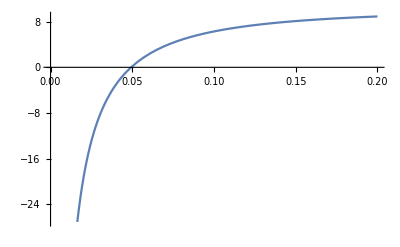

```mathematica
Plot[Pi*(i-Log[x1/x2])/.{y1->0.1181/Pi,x1->91.18, x2->25}, {y2, 0, 0.2}]
```

```mathematica
AlphasExact[asMz /. NumDef, Mz/.NumDef,10, 3,4]
```

0.20018369730618291319

```mathematica
%50-%51
```

-0.00032786299645167149

```mathematica
CForm[i]
```

(7493*ArcTan((768 + 3863*y1)/(12.*Sqrt(19082))))/(162.*Sqrt(19082)) - (7493*ArcTan((768 + 3863*y2)/(12.*Sqrt(19082))))/(162.*Sqrt(19082)) + 
   (2*(9 + 16*y1*Log(y1) - 8*y1*Log(864 + 1536*y1 + 3863*Power(y1,2))))/(81.*y1) - (2*(9 + 16*y2*Log(y2) - 8*y2*Log(864 + 1536*y2 + 3863*Power(y2,2))))/(81.*y2)

### Derivative (needed for Netwon-Raphson root finder)

```mathematica
d =FullSimplify[D[i-Log[x1/x2],y2]]
```

192/(y2^2 (y2 (3863 y2+1536)+864))

```mathematica
N[d/.{y1->0.118/Pi,x1->91.18, x2->10, y2->10}]
```

4.7699×10^-6

```mathematica
CForm[d]
```

192/(Power(y2,2)*(864 + y2*(1536 + 3863*y2)))

## Approx (PDG)

```mathematica
betaruleApprox = {b0->b[1]/2,b1->b[2]/b[1],b2->b[3]/b[1],b3->b[4]/b[1]}/.betarule
```

{b0→9/4,b1→16/9,b2→3863/864,b3→2/9 (9 ((809 3)/1296+50065/20736)+(891 3)/32-3 ((1627 3)/864+1078361/20736)+1349963/6912)}

```mathematica
pdgConst = {L->Log[x^2/Λ^2]/.Λ->0.332}
```

{L→log(9.07243 x^2)}

```mathematica
α[x_]= FullSimplify[Pi*(1/(b0*L)-(b1*Log[L])/(b0*L)^2+1/(b0*L)^3*(b1^2*(Log[L]^2-Log[L]-1)+b2)
+1/(b0*L)^4*(b1^3*(-Log[L]^3+5/2*Log[L]^2+2*Log[L]-1/2)-3*b1*b2*Log[L]+b3/2))/.pdgConst/.betaruleApprox];
```

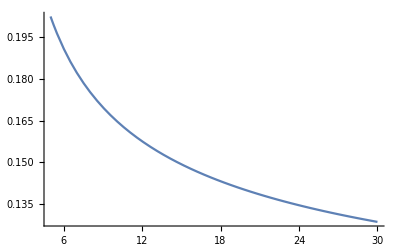

```mathematica
Plot[α[x], {x, 5, 30}]
```

```mathematica
α[5]
```

0.20257

```mathematica
α[20]
```

0.139888

```mathematica
α[30]
```

0.128537

```mathematica
AlphasLam[0.332,5,3,4]
```

0.20257

```mathematica
AlphasLam[0.332,10,3,4]
```

0.165139

```mathematica
AlphasLam[0.332,50,3,4]
```

0.116702

```mathematica
NumberForm[0.022766046055006255,15]
```

```mathematica
"0.0227660460550063"*Pi
```

0.0715216

```mathematica
NumDef
```

{asMz→0.118,Mz→91.18,Mt→175,Mb→4.7,Mc→1.6,muc→1.2,mub→3.97,Mtau→1.777}

```mathematica
AlphasExact[0.1181, 91.18,25, 3,4]
```

0.15494032713370412536

```mathematica
AlphasLam[0.64,10,3,4]
```

0.200125

```mathematica
CForm[α[x]]
```

(16.71314886448282 + Log(Power(x,2))*(20.731909992671614 + Log(Power(x,2))*(9.23729030880304 + 1.3962634015954634*Log(Power(x,2)))) + 
     (-8.83285552360219 + (-5.7374135345463095 - 1.103220465458144*Log(Power(x,2)))*Log(Power(x,2)))*Log(2.205240620131297 + Log(Power(x,2))) + 
     (3.6441027182711707 + 0.8716803677693978*Log(Power(x,2)))*Power(Log(2.205240620131297 + Log(Power(x,2))),2) - 
     0.6887351053980427*Power(Log(2.205240620131297 + Log(Power(x,2))),3))/Power(2.205240620131297 + Log(Power(x,2)),4)

### Tests

```mathematica
NumDef
```

{asMz→0.118,Mz→91.18,Mt→175,Mb→4.7,Mc→1.6,muc→1.2,mub→3.97,Mtau→1.777}

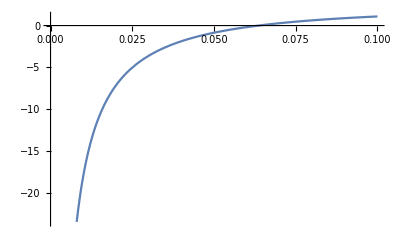

```mathematica
Plot[i-Log[x1/x2]/.{y1->0.118/Pi,x1->91.18,x2->10},{y2, 0, 0.1}]
```

```mathematica
0.06*Pi
```

0.188496

```mathematica
α[10]/Pi
```

0.00724666

```mathematica
FindRoot[x^2-7,{x,0.2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

{x→2.64575}

```mathematica
FindRoot[x^3-3,{x,0.1}]
```

{x→1.44225}

```mathematica
NumDef
```

{asMz→0.118,Mz→91.18,Mt→175,Mb→4.7,Mc→1.6,muc→1.2,mub→3.97,Mtau→1.777}

```mathematica
N[Zeta[7],15]
```

1.00834927738192